FittedModel[2187.41+0.0509686 x]

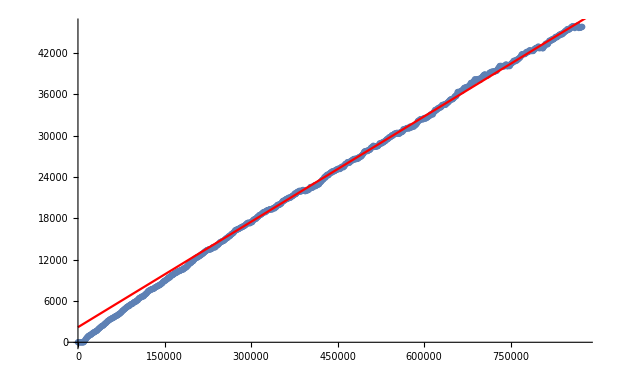

```mathematica
{60,0.04822125644909938,0.0012296876943978222};
s="D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalous\\MaxPower_L1500OT1000000_u60t100.txt";
data=ReadList[s,{Number,Number}];
f=LinearModelFit[Take[data,{Floor[0.5Length[data]],Length[data]}],{1,x},x]
Show[ListPlot[data],Plot[f[x],{x,0,10^6},PlotStyle->Red]]
```

```mathematica
data60={{1360.054938140121+0.0492927960020994 x},{1119.043189927865+0.05094836377937354 x},{1368.609474960411+0.052007348901782116 x},{141.0800120346123+0.05109877101863206 x},{1238.2872088347249+0.04768411883942077 x},{2017.518663021499+0.05228037227234776 x},{2787.7549642147264+0.05481378342095094 x},{2550.7558685892177+0.04988848605549063 x},{0},{1420.0485647776734+0.047264626264284196 x},{6194.738111035105+0.0463659311160627 x},{-5662.571434811994+0.04851713723911539 x},{-1698.6996662059157+0.05526845911319993 x},{-3109.0421542587765+0.051233538992198895 x},{-1153.1847655315098+0.05642125419796265 x},{-714.2917143223277+0.052667694557148675 x},{2187.4109799548705+0.050968624492861325 x}}/.{x->0};
```

FittedModel[1680.56+0.0677353 x]

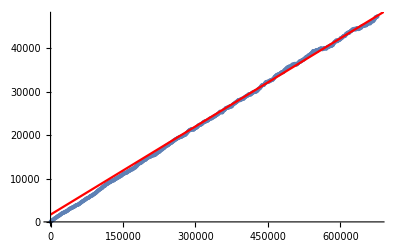

```mathematica
{30,0.07381192393818596,0.0022904842235867812};
s="D:\\Projects\\Iosel\\Calculus\\2D_Anomalous\\2D_Anomalous\\MaxPower_L1500OT1000000_u30t100.txt";
data=ReadList[s,{Number,Number}];
f=LinearModelFit[Take[data,{Floor[0.5Length[data]],Length[data]}],{1,x},x]
Show[ListPlot[data],Plot[f[x],{x,0,10^6},PlotStyle->Red]]
```

```mathematica
data30={{-1436.6655519621113+0.07769331958419265 x},{-3252.8371327784216+0.07622283654192813 x},{-438.742271997568+0.07258149442975408 x},{-716.8011072579562+0.07617345721713824 x},{-4801.514804970682+0.08004962730424414 x},{-380.49503824881117+0.07232958154428125 x},{2442.893079998332+0.06930080224309947 x},{-1562.6859834057195+0.07536585506873107 x},{-3007.34252942257+0.07863755215134673 x},{1736.4381624093453+0.0700824739456545 x},{-1665.052000931542+0.08153762784708286 x},{3153.6676889779674+0.06988603502693422 x},{-2454.15583488294+0.07723837157267938 x},{2364.807766922765+0.07152476561830297 x},{1845.636495177914+0.0720760376467782 x},{0.535054035355584-9.876661020588328*^-8 x},{4161.6115083315235+0.06781622617868646 x},{-718.9945685256978+0.07067864313630176 x},{489.84167404526954+0.07272471472090085 x},{1680.5564302144423+0.06773534843075678 x}}/.{x->0};
```

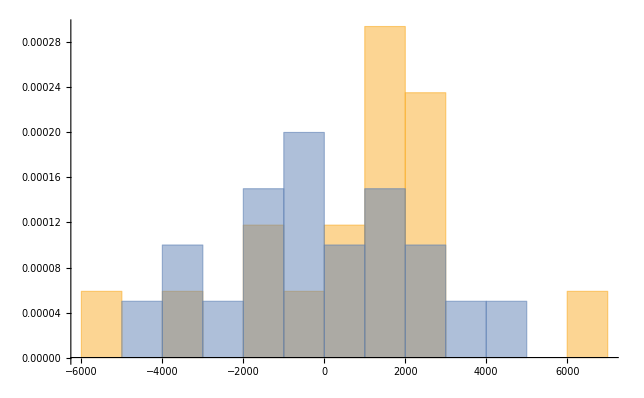

```mathematica
Histogram[{Flatten@data60,Flatten@data30},{1000},"PDF"]
```